```mathematica
Solve[g r + 1/2 Sqrt[5/2 g r]^2 == 1/2 vb^2,vb]
```

{{vb→-(3 √g √r)/(√2)},{vb→(3 √g √r)/(√2)}}

```mathematica
Solve[gr +  gr == 1/2 vb^2,vb]
```

{{vb→-2 √gr},{vb→2 √gr}}

```mathematica
Sqrt[2]*1.981
```

2.80156

```mathematica
curve = -g/(2 vo^2 Cos[α]^2)x^2 + Tan[α]x
```

-(g x^2 Sec[α]^2)/(2 vo^2)+x Tan[α]

```mathematica
curve/.{vo-> Sqrt[5g r/2],α-> ArcTan[2]}/.r-> 0.2
```

2 x-5. x^2

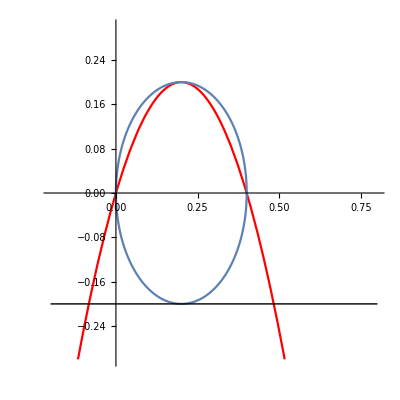

```mathematica
Show[Plot[curve/.{vo-> Sqrt[5g r/2],α-> ArcTan[2]}/.r-> 0.2,{x,-0.2,0.8},AspectRatio->1,PlotRange->{{-0.2,0.8},{-0.3,0.3}},PlotStyle->Red],ParametricPlot[{{Cos[θ]0.2+0.2,Sin[θ]*0.2}},{θ,0,2π},AspectRatio->1],ParametricPlot[{x,-0.2},{x,-0.2,0.8},PlotStyle->{Black,Thick}]]
```

```mathematica
Solve[{2r == (Sin[2α]vo^2)/g, r == (vo^2 Sin[α]^2)/(2g)},{vo,α}]
```

{{vo→-√(5/2) √g √r,α→ConditionalExpression[ArcTan[2]+2 π C[1],C[1]∈Integers]},{vo→-√(5/2) √g √r,α→ConditionalExpression[-π+ArcTan[2]+2 π C[1],C[1]∈Integers]},{vo→√(5/2) √g √r,α→ConditionalExpression[ArcTan[2]+2 π C[1],C[1]∈Integers]},{vo→√(5/2) √g √r,α→ConditionalExpression[-π+ArcTan[2]+2 π C[1],C[1]∈Integers]}}

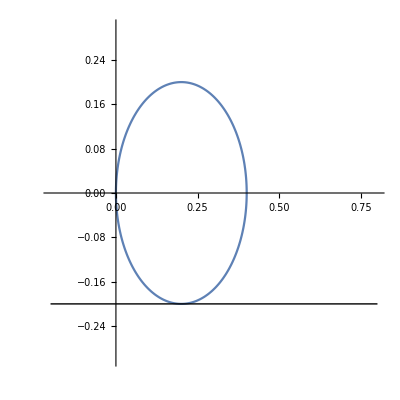

```mathematica
Show[Plot[-g/(2 vo^2 Cos[α]^2)x^2 + Tan[α]*x,{x,-0.2,0.8},AspectRatio->1,PlotRange->{{-0.2,0.8},{-0.3,0.3}},PlotStyle->Red]/.{vo-> Sqrt[5/2]*g * 0.2,α-> ArcTan[2]},ParametricPlot[{{Cos[θ]0.2+0.2,Sin[θ]*0.2}},{θ,0,2π},AspectRatio->1],ParametricPlot[{x,-0.2},{x,-0.2,0.8},PlotStyle->{Black,Thick}]]
```

```mathematica
3/Sqrt[2.]
```

2.12132

```mathematica
Sqrt[2(1+Sqrt[2.])]
```

2.19737